```mathematica
T=5761
```

5761

### Antibiotic treatment without corticosteroids

```mathematica
data = Import["C:\\Users\\juhaszn\\Documents\\HAL\\output\\StaphyloExperiments\\AntibioticsOnly\\2022-10-27_10-42-43tablets100.0__diff0.5__delaytime2880\\Out.csv","Data"];
```

Data: tick, healthy, infected, dead, bacteria, immune,  AB, CS

```mathematica
data[[2]]
```

{0,10000.,0.,0.,47.8599,0.9996,0.,0.}

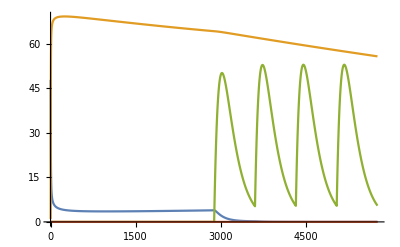

```mathematica
bactData=Table[data[[i]][[5]],{i,1,T}];
immuneData=Table[data[[i]][[6]],{i,1,T}];
ABData=Table[data[[i]][[7]],{i,1,T}];
CSData=Table[data[[i]][[8]],{i,1,T}];
ListLinePlot[{bactData,immuneData,ABData,CSData}]
```

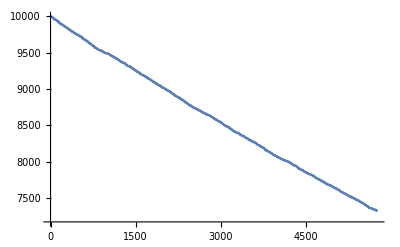

```mathematica
healthyCellData =Table[data[[i]][[2]],{i,1,T}];
ListLinePlot[{healthyCellData}]
```

### Antibiotic treatment with corticosteroids

```mathematica
dataCStrue = Import["C:\\Users\\juhaszn\\Documents\\HAL\\output\\StaphyloExperiments\\steroidBoostedAB\\2022-10-27_10-28-38tablets100.0__diff0.5__delaytime2880\\Out.csv","Data"];
```

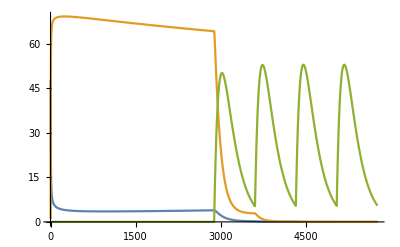

```mathematica
bactData=Table[dataCStrue[[i]][[5]],{i,1,T}];
immuneData=Table[dataCStrue[[i]][[6]],{i,1,T}];
ABData=Table[dataCStrue[[i]][[7]],{i,1,T}];
CSData=Table[dataCStrue[[i]][[8]],{i,1,T}];
ListLinePlot[{bactData,immuneData,ABData}]
```

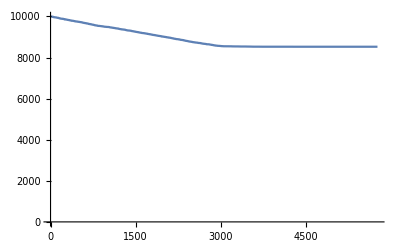

```mathematica
healthyCellData =Table[dataCStrue[[i]][[2]],{i,1,T}];
ListLinePlot[{healthyCellData},PlotRange->{0,10000}]
```